# Practica 1

## Ejercicio 1

Primero se importa la librería RandomData.m. Contiene funciones para crear numeros aleatorioscon distribución uniforme o exponencial. Se prueba que funcione.

Se crea una distribución uniforme con Histogram de un array de RandomData y una distriución exponencial con Histogram de RandomExp.

0.773033

0.00143182

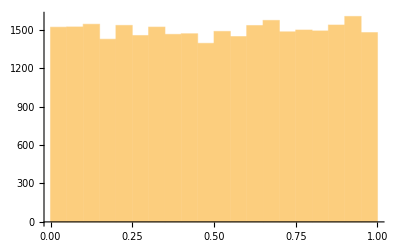

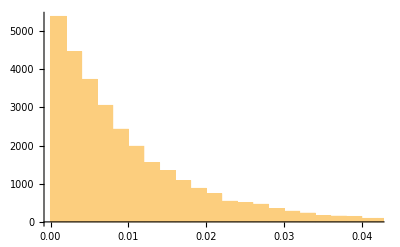

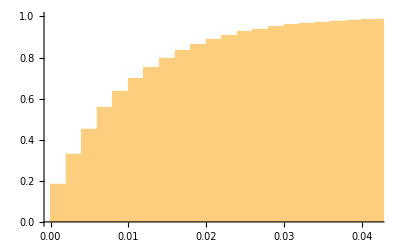

```mathematica
<< "/home/pablo/Escritorio/Uni/RRT/RandomData.m";
RandomData[]
RandomExp[100]
Histogram[Table[RandomData[],{30000}]]
Histogram[Table[RandomExp[100],{30000}]]
Histogram[Table[RandomExp[100],{30000}], 50,"CDF"]
```

## Ejercicio 2

Primero se codifica la función FifoSchedulling[]. Para una lista de llegadas y de tiempos de servicio, genera un array de tiempos de salida. Esto es, indica cada paquete en que momento va a salir de la linea (para saber cuando entra, tiempo de salida - tiempo de servicio), en función de los paquetes anteriores en el sistema y de su momento de llegada al sistema.

Se genera un array de numeros aleatorio que siguen una distribución exponencial (array entre llegadas al sistema). Su acumulación (array=[1,1+2,1+2+3,...,])lo consideramos como los tiempos de llegada de N paquetes al sistema. Se genera con otra media otro array de la misma longitud para los tiempos de servicio de cada paquete. Se calculan los tiempos de salida y se muestran varias gráficas.

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
nmax=1000;
mu=200;
ro=0.8;
lambda=mu*ro;
InterArrivalsTime=Table[RandomExp[lambda],{nmax}];
ArrivalsTime=Accumulate[InterArrivalsTime];
ServiceTime=Table[RandomExp[mu],{nmax}];
DepartureTime=FifoSchedulling[ArrivalsTime, ServiceTime];
```

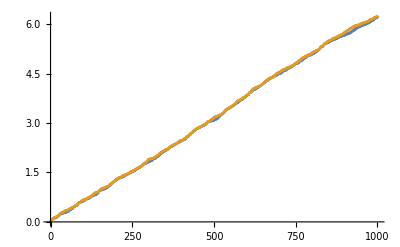

```mathematica
ListPlot[{ArrivalsTime,DepartureTime}]
```

```mathematica
Manipulate[ListPlot[{ArrivalsTime[[origin;;origin+width]],DepartureTime[[origin;;origin+width]]}],{origin,1,1000-width,1},{width,10,40,1}]
```

Part::take: Cannot take positions 1 through 11 in ArrivalsTime.

Part::take: Cannot take positions 1 through 11 in DepartureTime.

```mathematica
Manipulate[
ListStepPlot[{ArrivalsTime[[1;;width]],DepartureTime[[1;;width]]}],{width,10,40,1}]
```

Part::take: Cannot take positions 1 through 10 in ArrivalsTime.

Part::take: Cannot take positions 1 through 10 in DepartureTime.

Se dispone a calcular el numero de usuarios en el sistema. Para ello Se crean modifican los arrays de llegadas y salidas de modo que en cada tiempo de llegada y cada tiempo de salida se indique con claridad si entra o sale un usuario al sistema. Las llegadas ahora son {time,1} y las salidas {time,-1}. Se juntan y se calcula un acumulado de usuarios en el sistema. Se añade al final una función que calcula la probabilidad de X usuarios en el sistema.

```mathematica
ArrivalsEvent[lst_]:=Map[{#,1}&,lst]
DepartureEvent[lst_]:=Map[{#,-1}&,lst]
```

```mathematica
A=ArrivalsEvent[ArrivalsTime];
B=DepartureEvent[DepartureTime];
EventList=Sort[Join[A,B]];
```

```mathematica
DrawMountain[lst_]:=Module[{n=0,lastTime=0},Flatten[Map[{{lastTime,n},{lastTime=#[[1]],If[#[[2]]==1,n++,n--]}}&,lst],1]]
listStat=DrawMountain[EventList];
Manipulate[ListLinePlot[listStat[[1;;width]]],{width,10,1000,1}]
```

Part::take: Cannot take positions 1 through 10 in listStat.

ListLinePlot::lpn: listStat⟦1;;10⟧ is not a list of numbers or pairs of numbers.

Part::take: Cannot take positions 1 through 10 in listStat.

ListLinePlot::lpn: listStat⟦1;;10⟧ is not a list of numbers or pairs of numbers.

```mathematica
GetProb[n_,lst_]:=
Module[{time=0,lastTime=0},Map[(If[#[[2]]==n,time+=#[[1]]-lastTime];
lastTime=#[[1]])&,lst];
time/Last[lst][[1]]]
```

```mathematica
GetProb[0,listStat]+GetProb[1,listStat]+GetProb[2,listStat]+GetProb[3,listStat]+GetProb[4,listStat]+GetProb[5,listStat]+GetProb[6,listStat]+GetProb[7,listStat]
```

0.820018